```mathematica
Clear[c1,c2,R,S,k,kp,f1,f2,f3,f4,a,C10,C1a,C20,C2a];
f1=c1+c2-(1+R);
f2=c1-c2-k/kp (1-R);
f3=c1 Exp[I kp a]+c2 Exp[-I kp a]-S Exp[I k a];
f4=c1 Exp[I kp a] kp-c2 Exp[-I kp a] kp-S Exp[I k a] k;
C10=Collect[Solve[f1+f2==0,c1],R]
C20=Collect[Solve[f1-f2==0,c2],R]
C1a=Solve[f3+f4==0,c1]
C2a=Solve[((f3-f4)/.%)==0,c2]
Print[Style["c1 is:",Red,18]]
FullSimplify[Level[C1a,3][[2]]/.Level[C2a,2][[1]],Assumptions->{{S,k,kp,a}∈Reals&&k>0&& kp>0&&kp>k&&S>0}]
Print[Style["S,R is:",Red,18]]
FullSimplify[Solve[{(k+kp)/(2 kp)+((-k+kp) R)/(2 kp)==(ⅇ^(ⅈ a (k-kp)) (k+kp) S)/(2 kp),(-k+kp)/(2 kp)+((k+kp) R)/(2 kp)==-(ⅇ^(ⅈ a k+ⅈ a kp) (k-kp) S)/(2 kp)},{S,R}],Assumptions->{{R,S,k,kp,a}∈Reals&&k>0&& kp>0&&kp>k&&S>0&&R>0}]
Print[Style["|S|^2,|R|^2 are:",Red,18]]
FullSimplify[((2 ⅈ ⅇ^(-ⅈ a k) k kp)/(2 ⅈ k kp Cos[a kp]+(k^2+kp^2) Sin[a kp])) ((2 ⅈ ⅇ^(-ⅈ a k) k kp)/(2 ⅈ k kp Cos[a kp]+(k^2+kp^2) Sin[a kp]))*,Assumptions->{{R,S,k,kp,a}∈Reals&&k>0&& kp>0&&kp>k&&S>0&&R>0}]//TraditionalForm
FullSimplify[(((k-kp) (k+kp) Sin[a kp])/(2 ⅈ k kp Cos[a kp]+(k^2+kp^2) Sin[a kp])) Conjugate[((k-kp) (k+kp) Sin[a kp])/(2 ⅈ k kp Cos[a kp]+(k^2+kp^2) Sin[a kp])],Assumptions->{{R,S,k,kp,a}∈Reals&&k>0&& kp>0&&kp>k&&S>0&&R>0}]//TraditionalForm
```

{{c1→(k+kp)/(2 kp)+((-k+kp) R)/(2 kp)}}

{{c2→(-k+kp)/(2 kp)+((k+kp) R)/(2 kp)}}

{{c1→(ⅇ^(-2 ⅈ a kp) (-c2+c2 kp+ⅇ^(ⅈ a k+ⅈ a kp) S+ⅇ^(ⅈ a k+ⅈ a kp) k S))/(1+kp)}}

{{c2→-(ⅇ^(ⅈ a k+ⅈ a kp) (k-kp) S)/(2 kp)}}

c1 is:

(ⅇ^(ⅈ a (k-kp)) (k+kp) S)/(2 kp)

S,R is:

{{S→(2 ⅈ ⅇ^(-ⅈ a k) k kp)/(2 ⅈ k kp Cos[a kp]+(k^2+kp^2) Sin[a kp]),R→((k-kp) (k+kp) Sin[a kp])/(2 ⅈ k kp Cos[a kp]+(k^2+kp^2) Sin[a kp])}}

|S|^2,|R|^2 are:

1/(((k^2+kp^2)^2 sin^2(a kp))/(4 k^2 kp^2)+cos^2(a kp))

((k^2-kp^2)^2 sin^2(a kp))/((k^2+kp^2)^2 sin^2(a kp)+4 k^2 kp^2 cos^2(a kp))

```mathematica
Clear[c1,c2,R,S,k,kp,f1,f2,f3,f4,a,C10,C1a,C20,C2a];
```

```mathematica
Clear[c1,c2,R,S,k,kp,f1,f2,f3,f4,a,C10,C1a,C20,C2a];
FullSimplify[Solve[{(k+kp)/(2 kp)+((-k+kp) R)/(2 kp)==(ⅇ^(-2 ⅈ a kp) (-c2+c2 kp+ⅇ^(ⅈ a k+ⅈ a kp) S+ⅇ^(ⅈ a k+ⅈ a kp) k S))/(1+kp),(-k+kp)/(2 kp)+((k+kp) R)/(2 kp)==(ⅇ^(ⅈ a kp) (-c1 ⅇ^(ⅈ a kp)+c1 ⅇ^(ⅈ a kp) kp+ⅇ^(ⅈ a k) S-ⅇ^(ⅈ a k) k S))/(1+kp)},{R,S}],Assumptions->{{k,kp,a}∈Reals&&k>0&& kp>0&&kp>k}]
```

{{R→(-(-1+ⅇ^(2 ⅈ a kp)) k^2 (1+kp)+ⅇ^(2 ⅈ a kp) kp (1+2 c1 (-1+kp)+kp)-kp (1+2 c2 (-1+kp)+kp)+k (-1+kp) (-1-kp+2 c2 kp+ⅇ^(2 ⅈ a kp) (-1-kp+2 c1 kp)))/((1+kp) (ⅇ^(2 ⅈ a kp) (-1+k) (-k+kp)+(1+k) (k+kp))),S→(ⅇ^(-ⅈ a (k+2 kp)) (c1 ⅇ^(4 ⅈ a kp) (k-kp) (-1+kp)-2 ⅇ^(2 ⅈ a kp) k (1+kp)+c2 (-1+kp) (k+kp)))/(2 (-k (1+kp) Cos[a kp]+ⅈ (k^2+kp) Sin[a kp]))}}

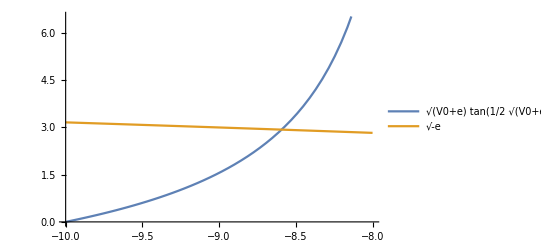

-8.7663

```mathematica
Clear[c1,c2,R,S,k,kp,f1,f2,f3,f4,a,V0,e];
V0=10;a=2.0;
Plot[{√(V0+e) Tan[(√(V0+e) a)/2],√-e},{e,-10,-8},PlotLegends->"Expressions"]
e1=-V0+π^2/(2 a^2)
```

```mathematica
Clear[c1,c2,R,S,k,kp,f1,f2,f3,f4,a,V0,e,V0,a];
V0=10;a=2.0;kp=1;
k= -1/I kp Tan[kp/2 a]
Cos[kp a]-I/2 (kp/k+k/kp) Sin[kp a]
```

0.+1.55741 ⅈ

5.55112×10^-17+0. ⅈ

```mathematica
Clear[ylna,ylpa,y,A,B,C1,C3,L,x,k,kp,a,eq1,eq2,eq3,eq4];
ylna=C1 Sin[k(-L-x)];
ylpa=C3 Sin[k  (L-x)];
(*y=A Cos[kp x]+B Sin[kp x];*)
y=A Cos[kp x];

eq1=(ylna/.x->-a)-(y/.x->-a);
eq1//TraditionalForm
eq2=(D[ylna,x]/.x->-a)-(D[y,x]/.x->-a);
eq2//TraditionalForm

eq3=(ylpa/.x->a)-(y/.x->a);
eq3//TraditionalForm
eq4=(D[ylpa,x]/.x->a)-(D[y,x]/.x->a);
eq4//TraditionalForm

Solve[{eq3==0,eq4==0},{A,C3}]
(*Solve[eq1+eq3==0,A]
Solve[eq1-eq3==0,C1]
Solve[eq2+eq4==0,C1]
Solve[eq2-eq4==0,A]

Solve[((1/2 Sec[a kp] (C1 Sin[k (a-L)]+C3 Sin[k (-a+L)]))/.C1->C3 Csc[k (a-L)] Sin[k (-a+L)])==((-((C1 k Cos[k (a-L)]-C3 k Cos[k (-a+L)]) Csc[a kp])/(2 kp))/.C1->C3 Csc[k (a-L)] Sin[k (-a+L)]),C3]
(*Reduce[((-1/2 (C1 Cos[a k]-C3 Cos[a k]) Csc[a kp])/.C1->-C3)==(((Sec[a kp] (C1 k Sin[a k]-C3 k Sin[a k]))/(2 kp))/.C1->-C3)]

Print[Style["does it have zeros?",Red,18]]
a=1;V0=2;k=√λ;kp=√(kp+V0);
Plot[Cos[a k] Csc[a kp]+(k Sec[a kp] Sin[a k])/kp,{λ,0,10}]
Clear[a,V0,λ,kp,k];*)
```

C1 sin(k (a-L))-A cos(a kp)

-A kp sin(a kp)-C1 k cos(k (a-L))

C3 sin(k (L-a))-A cos(a kp)

A kp sin(a kp)-C3 k cos(k (L-a))

{{A→0,C3→0}}

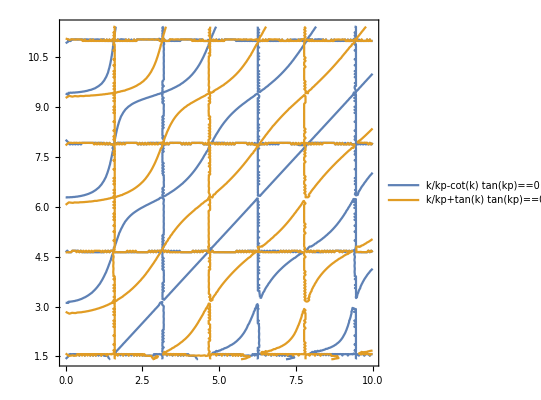

```mathematica
Clear[λ,V0,k,kp,a,f1,f2];
λ=1;V0=2;a=1;
f1=k/kp-Tan[kp a]/Tan[k a];
f2=Tan[kp a] Tan[k a]+k/kp;
(*ContourPlot[{f1==0},{k,0,5},{kp,√V0,5+√V0},PlotLegends->"Expressions"]
ContourPlot[{f2==0},{k,0,5},{kp,√V0,5+√V0},PlotLegends->"Expressions"]*)
ContourPlot[{f1==0,f2==0},{k,0,10},{kp,√V0,10+√V0},PlotLegends->"Expressions"]
```

```mathematica
Clear[ylna,ylpa,y,A,B,C2,C4,x,k,kp,a,eq1,eq2,eq3,eq4];
ylna=-C2 Sin[k x];
ylpa=C4 Sin[k x];
y=A Cos[kp x]+B Sin[kp x];

eq1=(ylna/.x->-a)-(y/.x->-a);
eq1//TraditionalForm
eq2=(D[ylna,x]/.x->-a)-(D[y,x]/.x->-a);
eq2//TraditionalForm

eq3=(ylpa/.x->a)-(y/.x->a);
eq3//TraditionalForm
eq4=(D[ylpa,x]/.x->a)-(D[y,x]/.x->a);
eq4//TraditionalForm

Solve[eq1+eq3==0,A]
Solve[eq1-eq3==0,B]
Solve[eq2+eq4==0,B]
Solve[eq2-eq4==0,A]



Solve[1/2 Sec[a kp] (C2 Sin[a k]+C4 Sin[a k])==-((C2 k Cos[a k]+C4 k Cos[a k]) Csc[a kp])/(2 kp),C2]
Reduce[{((-1/2 Csc[a kp] (C2 Sin[a k]-C4 Sin[a k]))/.C2->-C4)==((-((C2 k Cos[a k]-C4 k Cos[a k]) Sec[a kp])/(2 kp))/.C2->-C4)}]
```

-A cos(a kp)+B sin(a kp)+C2 sin(a k)

-A kp sin(a kp)-B kp cos(a kp)-C2 k cos(a k)

-A cos(a kp)-B sin(a kp)+C4 sin(a k)

A kp sin(a kp)-B kp cos(a kp)+C4 k cos(a k)

{{A→1/2 Sec[a kp] (C2 Sin[a k]+C4 Sin[a k])}}

{{B→-1/2 Csc[a kp] (C2 Sin[a k]-C4 Sin[a k])}}

{{B→-((C2 k Cos[a k]-C4 k Cos[a k]) Sec[a kp])/(2 kp)}}

{{A→-((C2 k Cos[a k]+C4 k Cos[a k]) Csc[a kp])/(2 kp)}}

{{C2→-C4}}

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{C4 Csc[a kp] Sin[a k]==(C4 k Cos[a k] Sec[a kp])/kp}]

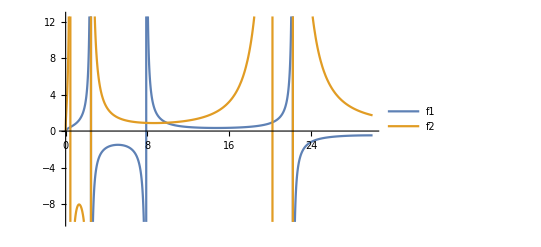

C4 Csc[√(2+λ)] Sin[√λ]

(C4 √λ Cos[√λ] Sec[√(2+λ)])/(√(2+λ))

```mathematica
Clear[λ,V0,k,kp,a,f1,f2];
V0=2;a=1;
k=√λ;kp=√(V0+λ);
f1=k/kp-Tan[k a]/Tan[kp a];
f2=Tan[kp a] Tan[k a]+k/kp;
Plot[{f1,f2},{λ,0,30},PlotLegends->"Expressions"]
-1/2 Csc[a kp] (C2 Sin[a k]-C4 Sin[a k])/.C2->-C4
-((C2 k Cos[a k]-C4 k Cos[a k]) Sec[a kp])/(2 kp)/.C2->-C4
```

-k Cot[k (-a+L)]

-η Tan[a η]

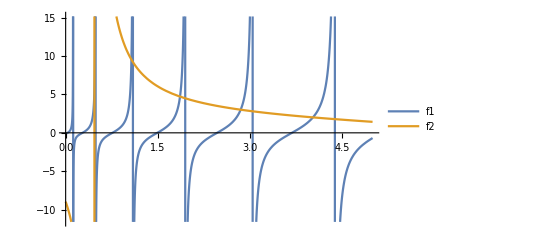

```mathematica
Clear[η,k,x,L,ylpa,y,a,f1,f2];
ylpa=B Sin[k (L-x)];
y=Cos[η x];
f1=(D[ylpa,x]/.x->a)/(ylpa/.x->a)
f2=(D[y,x]/.x->a)/(y/.x->a)
V0=2;a=1;L=10;
k=√λ;η=√(V0+λ);
Plot[{f1,f2},{λ,0,5},PlotLegends->"Expressions"]
```

-k Cot[k (-a+L)]

η Cot[a η]

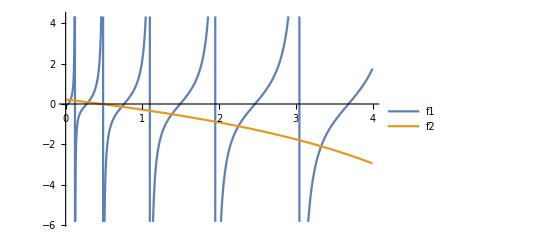

```mathematica
Clear[η,k,x,L,ylpa,y,a,f1,f2];
ylpa=B Sin[k (L-x)];
y=Sin[η x];
f1=(D[ylpa,x]/.x->a)/(ylpa/.x->a)
f2=(D[y,x]/.x->a)/(y/.x->a)
V0=2;a=1;L=10;
k=√λ;η=√(V0+λ);
Plot[{f1,f2},{λ,0,4},PlotLegends->"Expressions"]
```